Sampling

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

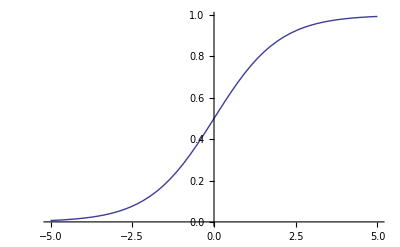

```mathematica
Plot[Logistic[x],{x,-5,5}]
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Sampling Functions

```mathematica
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
zsample[l_]:= (Sign[Thread[l - RandomReal[1, Length[l]]]]+1)/2;
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
HiddenProbabilities[w_][v_]:=Logistic[wᵀ.v];
VisibleProbabilities[w_][h_]:= Most[Logistic[w.h]];
```

## Learning

```mathematica
ClearAll[DataLearning,DeltaWeight]
```

```mathematica
DeltaWeight[ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew,v3,h3},
wnew=w;
Do[
h1=SampleHidden[w][v1];
v2=SampleVisible[w][h1];
h2=SampleHidden[w][v2];
v3=SampleVisible[w][h2];
h3=SampleHidden[w][v3];
(*
w0=1-Outer[BitXor, v1, h1];
w1=1-Outer[BitXor, v1, h3];*)
w0=Outer[Times, v1, h1];
w1=Outer[Times, v1, h3];

wnew += ϵ*(w0-w1);
,
{16}];
wnew
]
```

```mathematica
DataLearning[w_,ϵ_,n_,dataV_]:=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n]
```

```mathematica
StepLearning[w_,ϵ_,n_,dataV_]:=Module[{w1,w2,w3},w1=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n/3];
w2=Nest[Function[DeltaWeight[ϵ/10,RandomChoice[dataV]][#]],w1,n/3];
w3=Nest[Function[DeltaWeight[ϵ/100,RandomChoice[dataV]][#]],w2,n/3];
w3
]
```

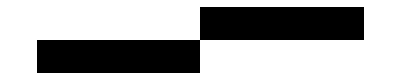

```mathematica
ArrayPlot[{{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}}]
```

## Testing

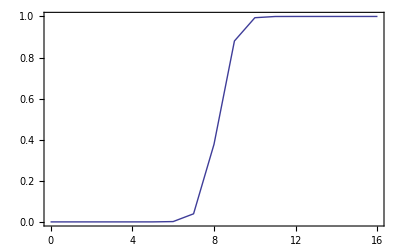

```mathematica
SeedRandom[5];
Hn=1;Vn=17;
W=RandomReal[{-0.5,0.5},{Vn,Hn}];
dataV=Append[#*2-1,1]& /@ {{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0}};
w1=StepLearning[W,0.002,4500,dataV];

m=Map[HiddenProbabilities[w1],Append[#,1]& /@Tuples[{-1,1},16]];
m1=Map[HammingDistance[{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1},#]&,Tuples[{0,1},16]];
pairs=Transpose[{m1,Flatten[m]}];
pairs2=Mean /@ GatherBy[pairs,First];
ListPlot[Sort[pairs2],PlotRange->{All,{0,1}},PlotRangePadding->0.1,Frame->True,Joined->True]
```

```mathematica
numbers2colors[Most[#]->HiddenProbabilities[w1][#]&/@dataV ]
numbers2colors[#-> VisibleProbabilities[w1][#]&/@Tuples[{-1,1},Hn]]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
square[col_]:=Graphics[Style[Rectangle[],col],ImageSize->10,Frame->True,FrameTicks->False];
numbers2colors[x_]:= x /. {-1 -> square[White], 1->square[Black], r_Real  :> Tooltip[square[Blend[{Red,White,Blue}, r]],r]};
```

```mathematica
colors[n_]:=Replace[Round[data[[1,n]]/256],0->-1,{2}]//numbers2colors
process1[n_]:=Flatten[Replace[Round[data[[1,n]]/256],0->-1,{2}]]
```